```mathematica
(*Będziemy definiować własne wersje dodawania oraz mnożenia dlatego musimy te definicje odbezpieczyć (Matehmatica ma zabezpiecza je przed przypadkowym przeładowaniem):*)
```

```mathematica
Unprotect[Plus];
```

```mathematica
Unprotect[Times];
```

```mathematica
(*Tworzymy przestrzeń liniową funkcji. Wektory (funkcje) z tej przestrzeni będą wyrażeniami typu function[expr , t], gdzie "t" jest argumentem funkcji a "expr" służy do liczenia wartości funkcji poprzez podstawienie odpowiedniej wartości "t".*)
```

```mathematica
function::usage = "function[expr , t]";
```

```mathematica
(*Mając funkcje w postaci function[expr , v] tak liczymy jej wartość dla danego "x":*)
```

```mathematica
function[expr_ , v_][x_]:=expr/.{v->x};
```

```mathematica
(*Tutaj definiujemy dodawanie funkcji:*)
```

```mathematica
function[expr1_ , v_] + function[expr2_ , v_]:= function[expr1 + expr2 , v];
```

```mathematica
(*Tutaj definiujemy mnożenie funkcji przez skalar:*)
```

```mathematica
x_ function[expr_ , v_]:= function[x expr , v];
```

```mathematica
(*Będziemy rozważać funkcje czasu:*)
```

```mathematica
t::usage = "Time";
```

```mathematica
(*Wstępna baza funkcji:*)
```

```mathematica
fun= {function[Sin[t] , t] , function[Cos[t],t]};
```

```mathematica
(*Bardzo pożyteczne funkcja licząca iloczyn skalarny wektorów - niedługo powinno się to pojawić na wykładzie. Będziemy z niej korzystać aby uczynić nasz wstępny wybór bazy "ortonormalnym". W nowej bazie wektory będą do siebie "prostopadłe" - w tym sensie, że ich iloczyn skalarny bedzie równy 0 oraz miały "długość" 1 (również policzona z wykorzystaniem iloczynu skalarnego).*)
```

```mathematica
sp[a_ , b_] := Integrate[a[t] b[t] , {t , 0 , 2 π}];
```

```mathematica
(*Korzystamy z funkcji Orthogonalize, naszej pierwotnej bazy "fun" orz naszej definicji iloczynu skalarnego "sp" aby policzyć "ortonormalną" bazę. Widać, że nowe funkcje różnią się jedynie stałym czynnikiem 1/(√π). Łatwo jest sprawdzić, że długość tych wektorów (policzna z wykorzystaniem naszej definicji iloczynu skalarnego) wynosi 1.*)
```

```mathematica
base = FullSimplify[Orthogonalize[fun , sp]]
```

{function[Sin[t]/(√π),t],function[Cos[t]/(√π),t]}

```mathematica
(*Przykładowa funkcja:*)
```

```mathematica
f = function[Sin[t] , t];
```

```mathematica
(*Możemy policzyc współrzędne tej funkcji w bazie "base" wykorzystująć naszą definicję iloczynu skalarnego "sp" (dlaczego to działa?):*)
```

```mathematica
repr = Table[FullSimplify[base[[i]]~sp~f] , {i , 1 , Dimensions[base][[1]]}]
```

{√π,0}

```mathematica
(*Tutaj sprawdzamy, czy rzeczywiście odtwarzamy "f" w bazie "base" ((a , b , c).{d , e , f} = {a d , b e , c , f}).*)
```

```mathematica
repr.base
```

function[Sin[t],t]

```mathematica
(*Teraz wybieramy bazę wielomianów maksymalnie 4 stopnia i definiujemy nowy iloczyn skalarny (o tej samej nazwie co poprzedni):*)
```

```mathematica
fun= {function[1 , t] , function[t , t] , function[t^2 , t] , function[t^3 , t] , function[t^4 , t]};
sp[a_ , b_] := Integrate[a[t] b[t] , {t , 0 , 1}];
```

```mathematica
(*Z wstępnego wyboru bazy "fun" tworzymy bazę "ortonormalną":*)
```

```mathematica
base = FullSimplify[Orthogonalize[fun , sp]]
```

{function[1,t],function[√3 (-1+2 t),t],function[√5 (1+6 (-1+t) t),t],function[√7 (-1+2 t) (1+10 (-1+t) t),t],function[3+30 (-1+t) t (2+7 (-1+t) t),t]}

```mathematica
(*Możemy sobie narysować wektory bazowe:*)
```

```mathematica
baseFunctions = Table[base[[ii]][t] , {ii , 1 , Dimensions[base][[1]]}]
```

{1,√3 (-1+2 t),√5 (1+6 (-1+t) t),√7 (-1+2 t) (1+10 (-1+t) t),3+30 (-1+t) t (2+7 (-1+t) t)}

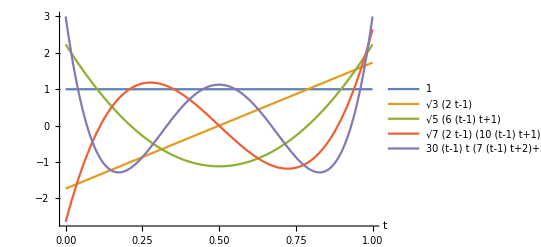

```mathematica
Plot[baseFunctions , {t , 0 , 1} , PlotRange->All , PlotStyle->Automatic , PlotLegends->baseFunctions , AxesLabel->{"t" , None}]
```

```mathematica
(*Teraz sprawdźmy, czy możemy w nowej bazie zapisać prosty wielomian:*)
```

```mathematica
f = function[3 t -4 , t];
```

```mathematica
(*Można poniższe wyrażenie odkomentować i sprawdzić co się stanie jeżeli w nowej bazie będziemy chcieli zapisać funkcję, która nie jest wielomianem 4 stopnia.*)
```

```mathematica
(*f = function[Sin[2 π t] , t];*)
```

```mathematica
repr = Table[FullSimplify[base[[i]]~sp~f] , {i , 1 , Dimensions[base][[1]]}]
```

{-5/2,(√3)/2,0,0,0}

```mathematica
(*Tutaj możemy sprawdzić, że rzeczywiście odtwarzamy wielomian:*)
```

```mathematica
repr.base//FullSimplify
```

function[-4+3 t,t]

```mathematica
(*Przybliżenia "f" z wykorzystaniem 1 , 2 , 3 , 4 oraz pięciu wektorów bazowych:*)
```

```mathematica
approx = Table[Sum[repr[[ii]] base[[ii]] , {ii , 1 , jj}][t] , {jj , 1 , Dimensions[base][[1]]}]//FullSimplify
```

{-5/2,-4+3 t,-4+3 t,-4+3 t,-4+3 t}

```mathematica
(*Rysunek funkcji (czarna linia przerywana) oraz przybliżeń:*)
```

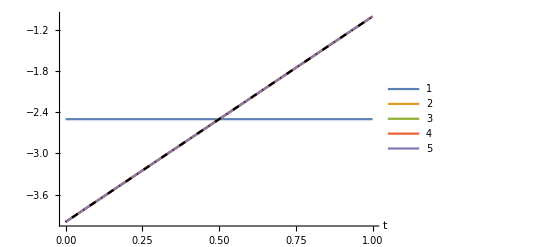

```mathematica
Show[Plot[approx , {t , 0 , 1} , PlotRange->All , PlotStyle->Automatic , PlotLegends->Range[Dimensions[base][[1]]] , AxesLabel->{"t" , None}] , Plot[f[t] , {t , 0 , 1} , PlotRange->All , PlotStyle->{Black , DotDashed}]]
```